## Define the sigmoid transfer function and its derivatives.

```mathematica
σ[z_]:=1/(1+ⅇ^-z)
```

```mathematica
D[σ[z],z]
```

ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
dσdz[z_]:=ⅇ^-z/((1+ⅇ^-z)^2)
```

```mathematica
D[σ[z],{z,2}]
```

(2 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
d2σdz2[z_]:=(2 ⅇ^(-2 z))/((1+ⅇ^-z)^3)-ⅇ^-z/((1+ⅇ^-z)^2)
```

```mathematica
D[σ[z],{z,3}]
```

(6 ⅇ^(-3 z))/((1+ⅇ^-z)^4)-(6 ⅇ^(-2 z))/((1+ⅇ^-z)^3)+ⅇ^-z/((1+ⅇ^-z)^2)

```mathematica
d3σdz3[z_]:=(6 ⅇ^(-3 z))/((1+ⅇ^-z)^4)-(6 ⅇ^(-2 z))/((1+ⅇ^-z)^3)+ⅇ^-z/((1+ⅇ^-z)^2)
```

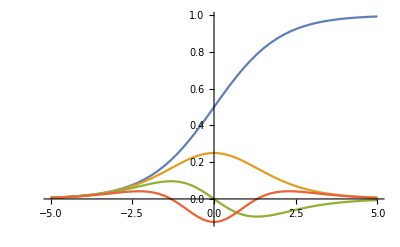

```mathematica
Plot[{σ[z],dσdz[z],d2σdz2[z],d3σdz3[z]},{z,-5,5},PlotRange->Full]
```